## Entorno

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
SetDirectory["Data"]
poblacion=Import["transport_zones_properties.csv"] ;
zonas0={{17},{17},{20},{23},{23},{24},{24},{28},{37},{38},{46},{64},{70},{72},{84},{88}};


municipios={};
Tpo=Transpose[poblacion];
For[i=2,i<Length[Tpo[[2]]],i++,If[Count[municipios,Tpo[[2]][[i]]]==0,AppendTo[municipios,Tpo[[2]][[i]]]]]

poblacion//MatrixForm;
zonesXmun=Flatten[Table[SequenceCases[Tpo[[2]],{p:Repeated[municipios[[i]]]}:>Length[{p}]],{i,1,Length[municipios]}]];
zonesXmun=Insert[zonesXmun,0,1];
muniindx=Table[{1+Sum[zonesXmun[[j]],{j,i}],Sum[zonesXmun[[j]],{j,i+1}]},{i,1,Length[municipios]}];
```

D:\Jose\Investigación\Sistemas complejos\Movilidad\Artículo sobre encuestas\Programas\Data

## Funciones y matrices generales

```mathematica
(*Funciones de modificación de matrices*)

	uniform[matrixdesun_]:= Transpose[Insert[Transpose[Insert[matrixdesun,Table[0,{k,1,118}],zonas0]],Table[0,{k,1,134}],zonas0]]

	compress[matrix_,mi_]:= Table[Table[∑_(m=mi[[j]][[1]])^(mi[[j]][[2]]) ∑_(n=mi[[i]][[1]])^(mi[[i]][[2]]) matrix[[n]][[m]],{j,1,15}],{i,1,15}]
```

```mathematica
(*Inicialización de matrices*)


encuesta=compress[Import["encuesta_Integer.dat",Path->"Encuesta"][[;;134,;;]],muniindx];
hw=compress[Import["Meanm_hw_st_week.csv",Path->"Saves"],muniindx];
allt=compress[Import["Meanm_allt_unst_all.csv",Path-> "Saves"],muniindx];
alltw=compress[Import["Meanm_allt_unst_week.csv",Path-> "Saves"],muniindx];
alltstw=compress[Import["Meanm_allt_st_week.csv",Path-> "Saves"],muniindx];
mo=compress[Import["Meanm_mo_unst_all.csv",Path-> "Saves"],muniindx];
mostw=compress[Import["Meanm_mo_st_week.csv",Path-> "Saves"],muniindx];

(*CUJAE*)
alltravelCUJAE=Import["movilidad_por_muniCUJAE.csv",Path->"Movilidad Municipal CUJAE"];
```

## Modelado con todos los viajes

Creación de modelo y cálculo de la verosimilitud

```mathematica
Probs=MapThread[Divide,{allt,Total[allt,{2}]}];

Verosimilitud[encList_,TotalVF_]:=(Log[Total[encList,{2}]!]-Total[Log[encList!],{2}]+Total[(encList)*Log[Probs/. 0.->10^-5],{2}])/(TotalVF/. 0.->1)
NewArtificialSurv[TotalPorFila_] :=(BinCounts[#,{0.5,15.5,1}]&)/@(MapIndexed[(RandomChoice[Probs[[#2[[1]]]]->Range[15],#1]&),TotalPorFila])
```

```mathematica
EncuestasPorZona=Total[encuesta,{2}];
VSurveyE=Table[Verosimilitud[NewArtificialSurv[EncuestasPorZona],EncuestasPorZona],100];
```

```mathematica
(*Encuesta*)

VEF=Verosimilitud[encuesta,EncuestasPorZona];

(*Casa trabajo*)
VxFhw=Total[hw,{2}];
Vhw=Verosimilitud[hw,VxFhw];

(*Allt inestables entre semana*)
VxFalltw=Total[alltw,{2}];
Valltw=Verosimilitud[alltw,VxFalltw];

(*Allt estables entre semana*)
VxFalltstw=Total[alltstw,{2}];
Valltstw=Verosimilitud[alltstw,VxFalltstw];

(*Mañana inestable*)
VxFmo=Total[mo,{2}];
Vmo=Verosimilitud[mo,VxFmo];

(*Mañana estable entre semana*)
VxFmostw=Total[mostw,{2}];
Vmostw=Verosimilitud[mostw,VxFmostw];

(*alltravelCUJAE*)
ViajesPorFilaAllCUJAE=Total[alltravelCUJAE,{2}];
VAllCUJAEF=Verosimilitud[alltravelCUJAE,ViajesPorFilaAllCUJAE];
```

Ploteo

```mathematica
GráficasT=Manipulate[ListLogPlot[-1*{VSurveyE[[A]],VEF,Vhw,Valltw,Valltstw,Vmo,Vmostw,VAllCUJAEF},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Todos los viajes (artificiales)"  ,"Encuesta", "Casa trabajo","Viajes entre semana","Viajes entre semana de estables","Viajes en la mañana","Viajes en la mañana entre semana de estables", "Todos los viajes CUJAE"}],{A,1,50}];

GráficasS=Manipulate[ListLogPlot[-1*{VSurveyE[[A]],VEF,Vhw,Valltw,Vmo},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Todos los viajes (artificiales)"  ,"Encuesta", "Casa trabajo","Viajes entre semana","Viajes en la mañana"}],{A,1,50}];

GráficasCUJAEND=Manipulate[ListLogPlot[-1*{VSurveyE[[A]],VEF,VAllCUJAEF},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Todos los viajes (artificiales/ND)"  ,"Encuesta", "Todos los viajes CUJAE"}],{A,1,50}];
```

```mathematica
(*Todos los datos*)
GráficasT
```

```mathematica
(*CUJAE*)
GráficasCUJAEND
```

```mathematica
(*Datos de buena verosimilitud*)
GráficasS
```

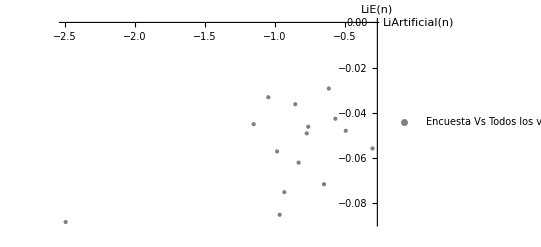

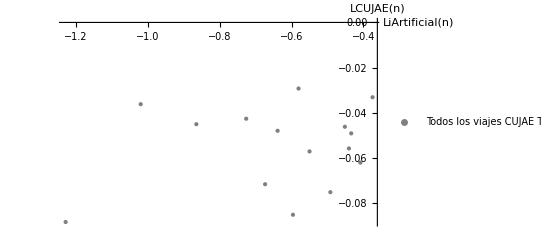

```mathematica
ListPlot[Table[{VEF[[i]],VSurveyE[[1]][[i]]},{i,1,15}],PlotRange->All,PlotStyle->{Gray,PointSize[Medium]}, AxesLabel->{LiArtificial[n],LiE[n]},PlotLegends->{"Encuesta Vs Todos los viajes (artificiales/ND)"}]

ListPlot[Table[{VAllCUJAEF[[i]],VSurveyE[[1]][[i]]},{i,1,15}],PlotRange->All, AxesLabel->{LiArtificial[n],LCUJAE[n]},PlotLegends->{"Todos los viajes CUJAE Todos los viajes CUJAETodos los viajes (artificiales/ND)"},PlotStyle->{Gray,PointSize[Medium]}]
```

```mathematica
Fluxes[mat_]:=Total[mat]-Total[Transpose[mat]];
```

```mathematica
Total[Total[alltravel]]
```

```mathematica
1.2833719978929157*^6/14315
```

89.6523

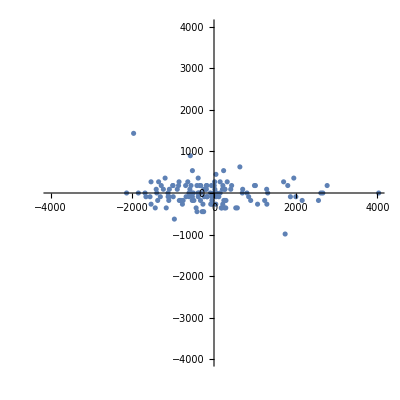

```mathematica
ListPlot[Transpose[{Fluxes[alltravel],Fluxes[89.6523*encuesta]}],PlotRange->{{-4000,4000},{-4000,4000}},AspectRatio->1]
```

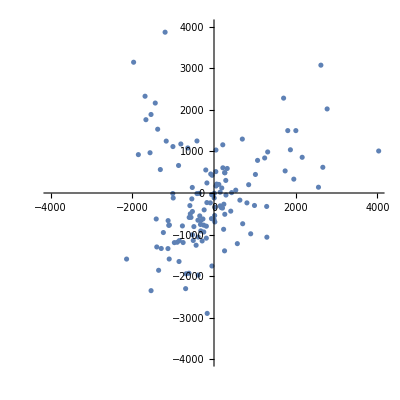

```mathematica
ListPlot[Transpose[{Fluxes[alltravel],Fluxes[alltravel69]}],PlotRange->{{-4000,4000},{-4000,4000}},AspectRatio->1]
```

## Modelado con casa trabajo

Creación de modelo y cálculo de la verosimilitud

```mathematica
HProbs=MapThread[Divide,{hw,Total[hw,{2}]}];

HVerosimilitud[encList_,TotalVF_]:=(Log[Total[encList,{2}]!]-Total[Log[encList!],{2}]+Total[(encList)*Log[HProbs/. 0.->10^-5],{2}])/(TotalVF/. 0.->1)
HNewArtificialSurv[TotalPorFila_] :=(BinCounts[#,{0.5,15.5,1}]&)/@(MapIndexed[(RandomChoice[HProbs[[#2[[1]]]]->Range[15],#1]&),TotalPorFila])
```

```mathematica
EncuestasPorZona=Total[encuesta,{2}];
HVSurveyE=Table[HVerosimilitud[HNewArtificialSurv[EncuestasPorZona],EncuestasPorZona],100];
```

```mathematica
(*Encuesta*)

HVEF=HVerosimilitud[encuesta,EncuestasPorZona];

(*Allt inestables*)
VxFallt=Total[allt,{2}];
HVallt=HVerosimilitud[allt,HVxFallt];

(*Allt inestables entre semana*)
VxFalltw=Total[alltw,{2}];
HValltw=HVerosimilitud[alltw,VxFalltw];

(*Allt estables entre semana*)
VxFalltstw=Total[alltstw,{2}];
HValltstw=HVerosimilitud[alltstw,VxFalltstw];

(*Mañana inestable*)
VxFmo=Total[mo,{2}];
HVmo=HVerosimilitud[mo,VxFmo];

(*Mañana estable entre semana*)
VxFmostw=Total[mostw,{2}];
HVmostw=Verosimilitud[mostw,VxFmostw];

(*alltravelCUJAE*)
ViajesPorFilaAllCUJAE=Total[alltravelCUJAE,{2}];
HVAllCUJAEF=HVerosimilitud[alltravelCUJAE,ViajesPorFilaAllCUJAE];
```

Ploteo

```mathematica
GráficasT=Manipulate[ListLogPlot[-1*{HVSurveyE[[A]],HVEF,HVallt,HValltw,HValltstw,HVmo,HVmostw,HVAllCUJAEF},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Casa trabajo (artificiales)"  ,"Encuesta", "Todos los viajes","Viajes entre semana","Viajes entre semana de estables","Viajes en la mañana","Viajes en la mañana entre semana de estables", "Todos los viajes CUJAE"}],{A,1,50}];

GráficasS=Manipulate[ListLogPlot[-1*{HVSurveyE[[A]],HVEF,HVallt,HValltw,HValltstw,HVmostw},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Casa trabajo (artificiales)"  ,"Encuesta", "Todos los viajes","Viajes entre semana","Viajes de estables entre semana","Viajes en la mañana de estables entre semana"}],{A,1,50}];

GráficasCUJAEND=Manipulate[ListLogPlot[-1*{HVSurveyE[[A]],HVEF,HVAllCUJAEF},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Casa trabajo (artificiales)"  ,"Encuesta", "Todos los viajes CUJAE"}],{A,1,50}];
```

```mathematica
(*Todos los datos*)
GráficasT
```

```mathematica
(*CUJAE*)
GráficasCUJAEND
```

```mathematica
(*Datos de buena verosimilitud*)
GráficasS
```

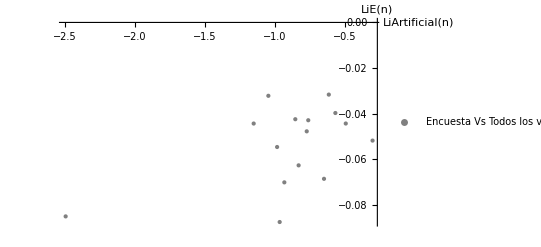

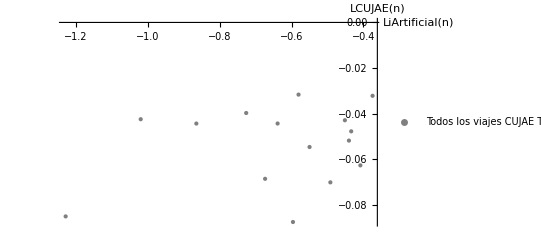

```mathematica
ListPlot[Table[{VEF[[i]],VSurveyE[[1]][[i]]},{i,1,15}],PlotRange->All,PlotStyle->{Gray,PointSize[Medium]}, AxesLabel->{LiArtificial[n],LiE[n]},PlotLegends->{"Encuesta Vs Todos los viajes (artificiales/ND)"}]

ListPlot[Table[{VAllCUJAEF[[i]],VSurveyE[[1]][[i]]},{i,1,15}],PlotRange->All, AxesLabel->{LiArtificial[n],LCUJAE[n]},PlotLegends->{"Todos los viajes CUJAE Todos los viajes CUJAETodos los viajes (artificiales/ND)"},PlotStyle->{Gray,PointSize[Medium]}]
```

```mathematica
Fluxes[mat_]:=Total[mat]-Total[Transpose[mat]];
```

```mathematica
Total[Total[alltravel]]
```

```mathematica
1.2833719978929157*^6/14315
```

89.6523

```mathematica
ListPlot[Transpose[{Fluxes[alltravel],Fluxes[89.6523*encuesta]}],PlotRange->{{-4000,4000},{-4000,4000}},AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Fluxes[alltravel],Fluxes[alltravel69]}],PlotRange->{{-4000,4000},{-4000,4000}},AspectRatio->1]
```

-Graphics-

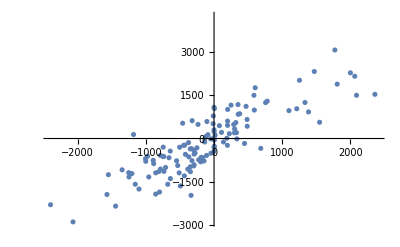

Thread::tdlen: Objects of unequal length in {{17.+Transpose[Insert[«3»]]⟦2⟧⟦3⟧+Transpose[Insert[«3»]]⟦3⟧⟦3⟧+Transpose[Insert[«3»]]⟦4⟧⟦3⟧+Transpose[Insert[«3»]]⟦5⟧⟦3⟧+Transpose[Insert[«3»]]⟦6⟧⟦3⟧+Transpose[Insert[«3»]]⟦7⟧⟦3⟧+Transpose[Insert[«3»]]⟦8⟧⟦3⟧+Transpose[Insert[«3»]]⟦9⟧⟦3⟧+Transpose[Insert[«3»]]⟦10⟧⟦3⟧+Transpose[Insert[«3»]]⟦11⟧⟦3⟧},«14»,{88.+Transpose[Insert[«3»]]⟦2⟧⟦3⟧+Transpose[Insert[«3»]]⟦3⟧⟦3⟧+Transpose[Insert[«3»]]⟦4⟧⟦3⟧+«4»+Transpose[Insert[«3»]]⟦9⟧⟦3⟧+Transpose[Insert[«3»]]⟦10⟧⟦3⟧+Transpose[Insert[«3»]]⟦11⟧⟦3⟧}}+«49»+«42» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1.].

Part::take: Cannot take positions 2 through -1 in 1..

Insert::psl: Position specification {17.} in Insert[Flatten[$Failed,1.]⟦2;;All,2;;All⟧,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«68»},{{17.},{17.},{20.},{23.},{23.},{24.},{24.},{28.},{37.},{38.},{46.},{64.},{70.},{72.},{84.},{88.}}] is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Insert::psl will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1.].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Part::take: Cannot take positions 2 through -1 in 1..

General::stop: Further output of Part::take will be suppressed during this calculation.

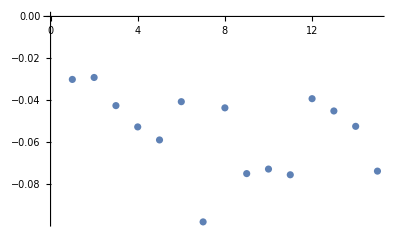

```mathematica
ListPlot[Transpose[{Fluxes[homework],Fluxes[alltravel69]}]]
```

## Modelado con viajes estables en la mañana entre semana

Creación de modelo y cálculo de la verosimilitud

```mathematica
Probs=MapThread[Divide,{mostw,Total[mostw,{2}]}];

Verosimilitud[encList_,TotalVF_]:=(Log[Total[encList,{2}]!]-Total[Log[encList!],{2}]+Total[(encList)*Log[Probs/. 0.->10^-5],{2}])/(TotalVF/. 0.->1)
NewArtificialSurv[TotalPorFila_] :=(BinCounts[#,{0.5,15.5,1}]&)/@(MapIndexed[(RandomChoice[Probs[[#2[[1]]]]->Range[15],#1]&),TotalPorFila])
```

```mathematica
EncuestasPorZona=Total[encuesta,{2}];
VSurveyE=Table[Verosimilitud[NewArtificialSurv[EncuestasPorZona],EncuestasPorZona],100];
```

```mathematica
(*Encuesta*)

VEF=Verosimilitud[encuesta,EncuestasPorZona];

(*Allt inestables*)
VxFallt=Total[allt,{2}];
Vallt=HVerosimilitud[allt,VxFallt];

(*Casa trabajo*)
VxFhw=Total[hw,{2}];
Vhw=Verosimilitud[hw,VxFhw];

(*Allt inestables entre semana*)
VxFalltw=Total[alltw,{2}];
Valltw=Verosimilitud[alltw,VxFalltw];

(*Allt estables entre semana*)
VxFalltstw=Total[alltstw,{2}];
Valltstw=Verosimilitud[alltstw,VxFalltstw];

(*Mañana inestable*)
VxFmo=Total[mo,{2}];
Vmo=Verosimilitud[mo,VxFmo];


(*alltravelCUJAE*)
ViajesPorFilaAllCUJAE=Total[alltravelCUJAE,{2}];
VAllCUJAEF=Verosimilitud[alltravelCUJAE,ViajesPorFilaAllCUJAE];
```

Ploteo

```mathematica
GráficasT=Manipulate[ListLogPlot[-1*{VSurveyE[[A]],VEF,Vallt,Vhw,Valltw,Valltstw,Vmo,VAllCUJAEF},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Viajes estables en la mañana entre semana (artificiales)"  ,"Encuesta","Todos los viajes" ,"Casa trabajo","Viajes entre semana","Viajes entre semana de estables","Viajes en la mañana", "Todos los viajes CUJAE"}],{A,1,50}];

GráficasS=Manipulate[ListLogPlot[-1*{VSurveyE[[A]],VEF,Vallt,Vhw,Valltw,Vmo},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Viajes estables en la mañana entre semana (artificiales)"  ,"Encuesta","Todos los viajes","Casa trabajo","Viajes entre semana","Viajes en la mañana"}],{A,1,50}];

GráficasCUJAEND=Manipulate[ListLogPlot[-1*{VSurveyE[[A]],VEF,VAllCUJAEF},PlotRange->All,PlotStyle->PointSize[Medium], AxesLabel->{n,-Li[n]},LabelStyle->Directive[Black,FontFamily->"Arial",12],PlotLegends->{"Viajes estables en la mañana entre semana (artificiales)"  ,"Encuesta", "Todos los viajes CUJAE"}],{A,1,50}];
```

```mathematica
(*Todos los datos*)
GráficasT
```

```mathematica
(*CUJAE*)
GráficasCUJAEND
```

```mathematica
(*Datos de buena verosimilitud*)
GráficasS
```

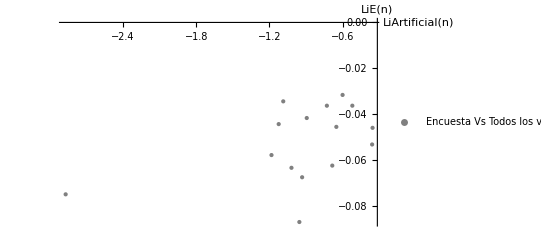

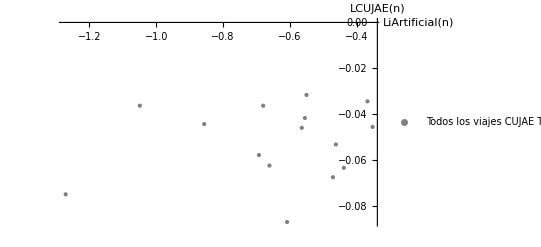

```mathematica
ListPlot[Table[{VEF[[i]],VSurveyE[[1]][[i]]},{i,1,15}],PlotRange->All,PlotStyle->{Gray,PointSize[Medium]}, AxesLabel->{LiArtificial[n],LiE[n]},PlotLegends->{"Encuesta Vs Todos los viajes (artificiales/ND)"}]

ListPlot[Table[{VAllCUJAEF[[i]],VSurveyE[[1]][[i]]},{i,1,15}],PlotRange->All, AxesLabel->{LiArtificial[n],LCUJAE[n]},PlotLegends->{"Todos los viajes CUJAE Todos los viajes CUJAETodos los viajes (artificiales/ND)"},PlotStyle->{Gray,PointSize[Medium]}]
```

```mathematica
Fluxes[mat_]:=Total[mat]-Total[Transpose[mat]];
```

```mathematica
Total[Total[alltravel]]
```

```mathematica
1.2833719978929157*^6/14315
```

89.6523

```mathematica
ListPlot[Transpose[{Fluxes[alltravel],Fluxes[89.6523*encuesta]}],PlotRange->{{-4000,4000},{-4000,4000}},AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Fluxes[alltravel],Fluxes[alltravel69]}],PlotRange->{{-4000,4000},{-4000,4000}},AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[Transpose[{Fluxes[homework],Fluxes[alltravel69]}]]
```

-Graphics-

Thread::tdlen: Objects of unequal length in {{17.+Transpose[Insert[«3»]]⟦2⟧⟦3⟧+Transpose[Insert[«3»]]⟦3⟧⟦3⟧+Transpose[Insert[«3»]]⟦4⟧⟦3⟧+Transpose[Insert[«3»]]⟦5⟧⟦3⟧+Transpose[Insert[«3»]]⟦6⟧⟦3⟧+Transpose[Insert[«3»]]⟦7⟧⟦3⟧+Transpose[Insert[«3»]]⟦8⟧⟦3⟧+Transpose[Insert[«3»]]⟦9⟧⟦3⟧+Transpose[Insert[«3»]]⟦10⟧⟦3⟧+Transpose[Insert[«3»]]⟦11⟧⟦3⟧},«14»,{88.+Transpose[Insert[«3»]]⟦2⟧⟦3⟧+Transpose[Insert[«3»]]⟦3⟧⟦3⟧+Transpose[Insert[«3»]]⟦4⟧⟦3⟧+«4»+Transpose[Insert[«3»]]⟦9⟧⟦3⟧+Transpose[Insert[«3»]]⟦10⟧⟦3⟧+Transpose[Insert[«3»]]⟦11⟧⟦3⟧}}+«49»+«42» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1.].

Part::take: Cannot take positions 2 through -1 in 1..

Insert::psl: Position specification {17.} in Insert[Flatten[$Failed,1.]⟦2;;All,2;;All⟧,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«68»},{{17.},{17.},{20.},{23.},{23.},{24.},{24.},{28.},{37.},{38.},{46.},{64.},{70.},{72.},{84.},{88.}}] is not a machine-sized integer or a list of machine-sized integers.

General::stop: Further output of Insert::psl will be suppressed during this calculation.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed,1.].

General::stop: Further output of Flatten::normal will be suppressed during this calculation.

Part::take: Cannot take positions 2 through -1 in 1..

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-